# Neural Network Explorations

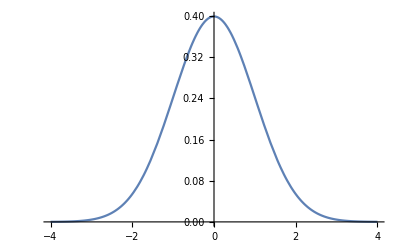

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]
```

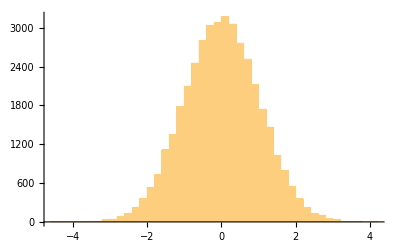

```mathematica
Histogram[RandomVariate[NormalDistribution[0,1],40000],50]
```

```mathematica
sample[center_,num_]:=RandomVariate[MultinormalDistribution[center,IdentityMatrix[2]],num]
```

```mathematica
sample[{1,1},3]
```

{{0.761655,0.534918},{1.90393,2.25122},{-1.09253,1.25704}}

```mathematica
clusters={sample[{-2,-2},10000],sample[{-2,2},10000],sample[{2,2},10000],sample[{2,-2},10000]};
```

```mathematica
Length[clusters]
```

4

```mathematica
MapThread[f,{{1,2,3},{a,b,c}}]
```

{f[1,a],f[2,b],f[3,c]}

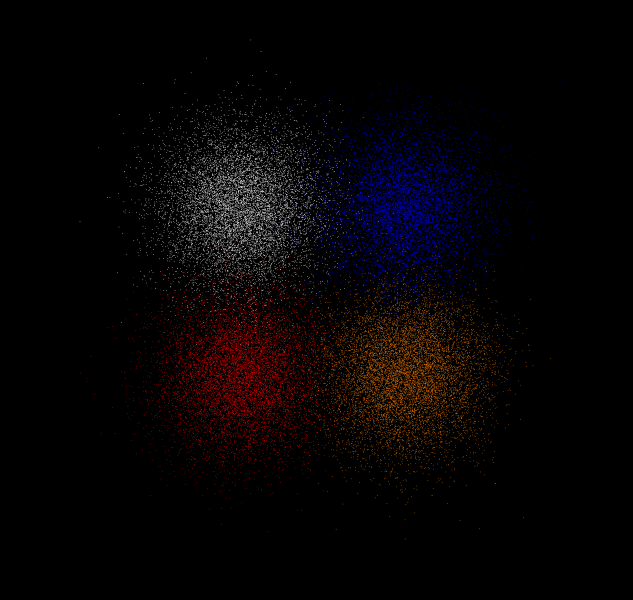

```mathematica
Graphics[{AbsolutePointSize[0.5],
MapThread[{#1,Point[#2]}&,{{Red,White,Blue,Orange},clusters}]
},
Background->Black,
PlotRange->10,
Axes->True
]
```

```mathematica
net=NetChain[{
DotPlusLayer[400],
ElementwiseLayer[Ramp],
DotPlusLayer[4],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{Red,White,Blue,Orange}}]
]
```

NetChain[]

```mathematica
NetGraph[net]
```

NetGraph[]

```mathematica
net=NetInitialize[net]
```

NetChain[]

```mathematica
clusters[[1,1]]
```

{-1.63456,-1.23428}

```mathematica
{-2.8142142826091465,-1.7651886006540418}->Red
```

{-2.81421,-1.76519}→RGBColor[1, 0, 0]

```mathematica
Thread[{{x1,y1},{x2,y2},{x3,y3}}->Red]
```

{{x1,y1}→RGBColor[1, 0, 0],{x2,y2}→RGBColor[1, 0, 0],{x3,y3}→RGBColor[1, 0, 0]}

```mathematica
data=RandomSample[
Join@@MapThread[
Thread[#1->#2]&,
{clusters,{Red,White,Blue,Orange}}]];
```

```mathematica
Take[data,20]//Column
```

{2.1609,-1.39936}→RGBColor[1, 0.5, 0]
{2.22174,3.24524}→RGBColor[0, 0, 1]
{2.08532,-3.4426}→RGBColor[1, 0.5, 0]
{2.70202,2.56429}→RGBColor[0, 0, 1]
{3.37708,1.52493}→RGBColor[0, 0, 1]
{-2.74439,-2.3586}→RGBColor[1, 0, 0]
{-1.43049,2.62943}→GrayLevel[1]
{3.34996,-2.29463}→RGBColor[1, 0.5, 0]
{1.02175,-0.736851}→RGBColor[1, 0.5, 0]
{-1.68309,-2.69144}→RGBColor[1, 0, 0]
{-2.00994,-3.06896}→RGBColor[1, 0, 0]
{2.28668,-2.0044}→RGBColor[1, 0.5, 0]
{-3.53504,1.44603}→GrayLevel[1]
{-1.26557,2.91285}→GrayLevel[1]
{1.15191,-1.06183}→RGBColor[1, 0.5, 0]
{-1.46236,0.642125}→RGBColor[1, 0, 0]
{-2.09072,-2.21064}→RGBColor[1, 0, 0]
{-3.94854,-2.58129}→RGBColor[1, 0, 0]
{-0.53741,2.62233}→GrayLevel[1]
{2.0001,2.90853}→RGBColor[0, 0, 1]

```mathematica
Length[data]
```

40000

```mathematica
training=Take[data,38000];
validation=Take[data,-2000];
```

```mathematica
Length[training]
```

38000

```mathematica
Length[validation]
```

2000

```mathematica
result=NetTrain[net,training,MaxTrainingRounds->10000,ValidationSet->validation]
```

NetChain[]

```mathematica
result[{2,2}]
```

RGBColor[0, 0, 1]

```mathematica
result[{10,10}]
```

RGBColor[0, 0, 1]

```mathematica
result[{-2,-2}]
```

RGBColor[1, 0, 0]

```mathematica
result[{-2,2}]
```

GrayLevel[1]

```mathematica
result[{2,2}]
```

RGBColor[0, 0, 1]

```mathematica
result[{2,-2}]
```

RGBColor[1, 0.5, 0]

```mathematica
result[{0,0}]
```

RGBColor[1, 0.5, 0]

```mathematica
result[{0,0},"Probabilities"]
```

<|RGBColor[1, 0, 0]→0.215607,GrayLevel[1]→0.244497,RGBColor[0, 0, 1]→0.249924,RGBColor[1, 0.5, 0]→0.289971|>

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.9485

```mathematica
cm["Accuracy"]
```

0.9485

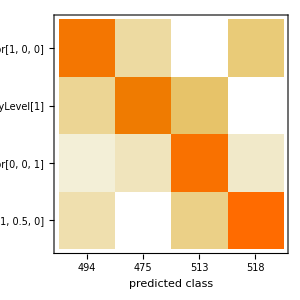

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm=ClassifierMeasurements[net,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.0765

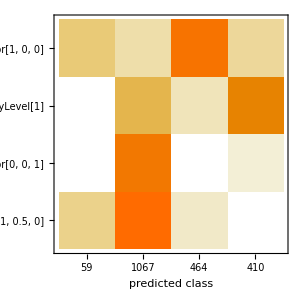

```mathematica
cm["ConfusionMatrixPlot"]
```